1.3.2. Наилучшее среднеквадратическое приближение

```mathematica
Clear[f,g,k,l,list1,list2,list3,list4,list5]
f[x_]:=Sin[k*x]
g[x_]:=Cos[l*x]
list1={};list2={};
Do[AppendTo[list1,Integrate[f[x],{x,0,2*Pi}]],{k,1,10}]
Do[AppendTo[list2,Integrate[g[x],{x,0,2*Pi}]],{l,1,10}]
list1
list2
```

{0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0}

```mathematica
list3={};
Do[Do[AppendTo[list3,Integrate[f[x]*g[x],{x,0,2*Pi}]],{l,1,10}],{k,1,10}]
list3
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
list4={};list5={};
Do[Do[AppendTo[list4,{l,k,Integrate[Sin[k*x]*Sin[l*x],{x,0,2*Pi}]}],{l,1,10}],{k,1,10}]
Do[Do[AppendTo[list5,{l,k,Integrate[Cos[k*x]*Cos[l*x],{x,0,2*Pi}]}],{l,1,10}],{k,1,10}]
list4
list5
```

{{1,1,π},{2,1,0},{3,1,0},{4,1,0},{5,1,0},{6,1,0},{7,1,0},{8,1,0},{9,1,0},{10,1,0},{1,2,0},{2,2,π},{3,2,0},{4,2,0},{5,2,0},{6,2,0},{7,2,0},{8,2,0},{9,2,0},{10,2,0},{1,3,0},{2,3,0},{3,3,π},{4,3,0},{5,3,0},{6,3,0},{7,3,0},{8,3,0},{9,3,0},{10,3,0},{1,4,0},{2,4,0},{3,4,0},{4,4,π},{5,4,0},{6,4,0},{7,4,0},{8,4,0},{9,4,0},{10,4,0},{1,5,0},{2,5,0},{3,5,0},{4,5,0},{5,5,π},{6,5,0},{7,5,0},{8,5,0},{9,5,0},{10,5,0},{1,6,0},{2,6,0},{3,6,0},{4,6,0},{5,6,0},{6,6,π},{7,6,0},{8,6,0},{9,6,0},{10,6,0},{1,7,0},{2,7,0},{3,7,0},{4,7,0},{5,7,0},{6,7,0},{7,7,π},{8,7,0},{9,7,0},{10,7,0},{1,8,0},{2,8,0},{3,8,0},{4,8,0},{5,8,0},{6,8,0},{7,8,0},{8,8,π},{9,8,0},{10,8,0},{1,9,0},{2,9,0},{3,9,0},{4,9,0},{5,9,0},{6,9,0},{7,9,0},{8,9,0},{9,9,π},{10,9,0},{1,10,0},{2,10,0},{3,10,0},{4,10,0},{5,10,0},{6,10,0},{7,10,0},{8,10,0},{9,10,0},{10,10,π}}

{{1,1,π},{2,1,0},{3,1,0},{4,1,0},{5,1,0},{6,1,0},{7,1,0},{8,1,0},{9,1,0},{10,1,0},{1,2,0},{2,2,π},{3,2,0},{4,2,0},{5,2,0},{6,2,0},{7,2,0},{8,2,0},{9,2,0},{10,2,0},{1,3,0},{2,3,0},{3,3,π},{4,3,0},{5,3,0},{6,3,0},{7,3,0},{8,3,0},{9,3,0},{10,3,0},{1,4,0},{2,4,0},{3,4,0},{4,4,π},{5,4,0},{6,4,0},{7,4,0},{8,4,0},{9,4,0},{10,4,0},{1,5,0},{2,5,0},{3,5,0},{4,5,0},{5,5,π},{6,5,0},{7,5,0},{8,5,0},{9,5,0},{10,5,0},{1,6,0},{2,6,0},{3,6,0},{4,6,0},{5,6,0},{6,6,π},{7,6,0},{8,6,0},{9,6,0},{10,6,0},{1,7,0},{2,7,0},{3,7,0},{4,7,0},{5,7,0},{6,7,0},{7,7,π},{8,7,0},{9,7,0},{10,7,0},{1,8,0},{2,8,0},{3,8,0},{4,8,0},{5,8,0},{6,8,0},{7,8,0},{8,8,π},{9,8,0},{10,8,0},{1,9,0},{2,9,0},{3,9,0},{4,9,0},{5,9,0},{6,9,0},{7,9,0},{8,9,0},{9,9,π},{10,9,0},{1,10,0},{2,10,0},{3,10,0},{4,10,0},{5,10,0},{6,10,0},{7,10,0},{8,10,0},{9,10,0},{10,10,π}}

```mathematica
Clear[i,j]

i=1;While[list4⟦i,1⟧==list4⟦i,1⟧&&i<Length@list4,i++]
i
j=1;
While[list5⟦j,1⟧==list5⟦j,1⟧&&j<Length@list5,j++]
j
```

100

100

```mathematica
(*Значиит интеграл от Sin[k*x]*Sin[l*x] и интеграл от Cos[k*x]*Cos[l*x] равны Pi, если l=k и равны 0, если l≠k, значит 1, Sin[x], Cos[x], Sin[2x], Cos[2x], ..., Sin[nx], Cos[nx] образуют ортогональную систему на отрезке [0;2*Pi]*)
```

```mathematica
Clear[r,k,x,newFun,a0,ak,bk]
r[x_]:=1+Sin[x/(2*Pi)]+Cos[x/(2*Pi)]+Sin[2 x/(2*Pi)]+Cos[2 x/(2*Pi)]+Sin[3 x/(2*Pi)]+Cos[3 x/(2*Pi)]+Sin[4 x/(2*Pi)]+Cos[4 x/(2*Pi)]+Sin[5 x/(2*Pi)]+Cos[5 x/(2*Pi)]
newFun[x_]:=a0/2+∑_(k=1)^5 (ak*Cos[(k*x)/2]+bk*Sin[(k*x)/2])
ak=1/(2*Pi)*Integrate[r[x]*Cos[(k*x)/2],{x,-2*Pi,2*Pi}]
bk=1/(2*Pi)*Integrate[(r[x]*Sin[(k*x)/2]),{x,-2*Pi,2*Pi}]
a0=1/(2*Pi)*Integrate[r[x],{x,0,2*Pi}]
```

1/(2 π)(-((π (Cos[k π]/(k π)+(ⅈ Sin[k π])/(k π)) (-14400 ⅈ+21076 ⅈ k^2 π^2-7645 ⅈ k^4 π^4+1023 ⅈ k^6 π^6-55 ⅈ k^8 π^8+ⅈ k^10 π^10+14400 k π Cos[1]+14400 ⅈ k^2 π^2 Cos[1]-6676 k^3 π^3 Cos[1]-6676 ⅈ k^4 π^4 Cos[1]+969 k^5 π^5 Cos[1]+969 ⅈ k^6 π^6 Cos[1]-54 k^7 π^7 Cos[1]-54 ⅈ k^8 π^8 Cos[1]+k^9 π^9 Cos[1]+ⅈ k^10 π^10 Cos[1]+7200 k π Cos[2]+3600 ⅈ k^2 π^2 Cos[2]-8738 k^3 π^3 Cos[2]-4369 ⅈ k^4 π^4 Cos[2]+1638 k^5 π^5 Cos[2]+819 ⅈ k^6 π^6 Cos[2]-102 k^7 π^7 Cos[2]-51 ⅈ k^8 π^8 Cos[2]+2 k^9 π^9 Cos[2]+ⅈ k^10 π^10 Cos[2]+4800 k π Cos[3]+1600 ⅈ k^2 π^2 Cos[3]-6492 k^3 π^3 Cos[3]-2164 ⅈ k^4 π^4 Cos[3]+1827 k^5 π^5 Cos[3]+609 ⅈ k^6 π^6 Cos[3]-138 k^7 π^7 Cos[3]-46 ⅈ k^8 π^8 Cos[3]+3 k^9 π^9 Cos[3]+ⅈ k^10 π^10 Cos[3]+3600 k π Cos[4]+900 ⅈ k^2 π^2 Cos[4]-5044 k^3 π^3 Cos[4]-1261 ⅈ k^4 π^4 Cos[4]+1596 k^5 π^5 Cos[4]+399 ⅈ k^6 π^6 Cos[4]-156 k^7 π^7 Cos[4]-39 ⅈ k^8 π^8 Cos[4]+4 k^9 π^9 Cos[4]+ⅈ k^10 π^10 Cos[4]+2880 k π Cos[5]+576 ⅈ k^2 π^2 Cos[5]-4100 k^3 π^3 Cos[5]-820 ⅈ k^4 π^4 Cos[5]+1365 k^5 π^5 Cos[5]+273 ⅈ k^6 π^6 Cos[5]-150 k^7 π^7 Cos[5]-30 ⅈ k^8 π^8 Cos[5]+5 k^9 π^9 Cos[5]+ⅈ k^10 π^10 Cos[5]+14400 ⅈ Cos[2 k π]-21076 ⅈ k^2 π^2 Cos[2 k π]+7645 ⅈ k^4 π^4 Cos[2 k π]-1023 ⅈ k^6 π^6 Cos[2 k π]+55 ⅈ k^8 π^8 Cos[2 k π]-ⅈ k^10 π^10 Cos[2 k π]+(7200-7200 ⅈ) k π Cos[1-2 k π]+(7200-7200 ⅈ) k^2 π^2 Cos[1-2 k π]-(3338-3338 ⅈ) k^3 π^3 Cos[1-2 k π]-(3338-3338 ⅈ) k^4 π^4 Cos[1-2 k π]+(969/2-(969 ⅈ)/2) k^5 π^5 Cos[1-2 k π]+(969/2-(969 ⅈ)/2) k^6 π^6 Cos[1-2 k π]-(27-27 ⅈ) k^7 π^7 Cos[1-2 k π]-(27-27 ⅈ) k^8 π^8 Cos[1-2 k π]+(1/2-ⅈ/2) k^9 π^9 Cos[1-2 k π]+(1/2-ⅈ/2) k^10 π^10 Cos[1-2 k π]+(3600-3600 ⅈ) k π Cos[2-2 k π]+(1800-1800 ⅈ) k^2 π^2 Cos[2-2 k π]-(4369-4369 ⅈ) k^3 π^3 Cos[2-2 k π]-(4369/2-(4369 ⅈ)/2) k^4 π^4 Cos[2-2 k π]+(819-819 ⅈ) k^5 π^5 Cos[2-2 k π]+(819/2-(819 ⅈ)/2) k^6 π^6 Cos[2-2 k π]-(51-51 ⅈ) k^7 π^7 Cos[2-2 k π]-(51/2-(51 ⅈ)/2) k^8 π^8 Cos[2-2 k π]+(1-ⅈ) k^9 π^9 Cos[2-2 k π]+(1/2-ⅈ/2) k^10 π^10 Cos[2-2 k π]+(2400-2400 ⅈ) k π Cos[3-2 k π]+(800-800 ⅈ) k^2 π^2 Cos[3-2 k π]-(3246-3246 ⅈ) k^3 π^3 Cos[3-2 k π]-(1082-1082 ⅈ) k^4 π^4 Cos[3-2 k π]+(1827/2-(1827 ⅈ)/2) k^5 π^5 Cos[3-2 k π]+(609/2-(609 ⅈ)/2) k^6 π^6 Cos[3-2 k π]-(69-69 ⅈ) k^7 π^7 Cos[3-2 k π]-(23-23 ⅈ) k^8 π^8 Cos[3-2 k π]+(3/2-(3 ⅈ)/2) k^9 π^9 Cos[3-2 k π]+(1/2-ⅈ/2) k^10 π^10 Cos[3-2 k π]+(1800-1800 ⅈ) k π Cos[4-2 k π]+(450-450 ⅈ) k^2 π^2 Cos[4-2 k π]-(2522-2522 ⅈ) k^3 π^3 Cos[4-2 k π]-(1261/2-(1261 ⅈ)/2) k^4 π^4 Cos[4-2 k π]+(798-798 ⅈ) k^5 π^5 Cos[4-2 k π]+(399/2-(399 ⅈ)/2) k^6 π^6 Cos[4-2 k π]-(78-78 ⅈ) k^7 π^7 Cos[4-2 k π]-(39/2-(39 ⅈ)/2) k^8 π^8 Cos[4-2 k π]+(2-2 ⅈ) k^9 π^9 Cos[4-2 k π]+(1/2-ⅈ/2) k^10 π^10 Cos[4-2 k π]+(1440-1440 ⅈ) k π Cos[5-2 k π]+(288-288 ⅈ) k^2 π^2 Cos[5-2 k π]-(2050-2050 ⅈ) k^3 π^3 Cos[5-2 k π]-(410-410 ⅈ) k^4 π^4 Cos[5-2 k π]+(1365/2-(1365 ⅈ)/2) k^5 π^5 Cos[5-2 k π]+(273/2-(273 ⅈ)/2) k^6 π^6 Cos[5-2 k π]-(75-75 ⅈ) k^7 π^7 Cos[5-2 k π]-(15-15 ⅈ) k^8 π^8 Cos[5-2 k π]+(5/2-(5 ⅈ)/2) k^9 π^9 Cos[5-2 k π]+(1/2-ⅈ/2) k^10 π^10 Cos[5-2 k π]+(7200+7200 ⅈ) k π Cos[1+2 k π]-(7200+7200 ⅈ) k^2 π^2 Cos[1+2 k π]-(3338+3338 ⅈ) k^3 π^3 Cos[1+2 k π]+(3338+3338 ⅈ) k^4 π^4 Cos[1+2 k π]+(969/2+(969 ⅈ)/2) k^5 π^5 Cos[1+2 k π]-(969/2+(969 ⅈ)/2) k^6 π^6 Cos[1+2 k π]-(27+27 ⅈ) k^7 π^7 Cos[1+2 k π]+(27+27 ⅈ) k^8 π^8 Cos[1+2 k π]+(1/2+ⅈ/2) k^9 π^9 Cos[1+2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[1+2 k π]+(3600+3600 ⅈ) k π Cos[2+2 k π]-(1800+1800 ⅈ) k^2 π^2 Cos[2+2 k π]-(4369+4369 ⅈ) k^3 π^3 Cos[2+2 k π]+(4369/2+(4369 ⅈ)/2) k^4 π^4 Cos[2+2 k π]+(819+819 ⅈ) k^5 π^5 Cos[2+2 k π]-(819/2+(819 ⅈ)/2) k^6 π^6 Cos[2+2 k π]-(51+51 ⅈ) k^7 π^7 Cos[2+2 k π]+(51/2+(51 ⅈ)/2) k^8 π^8 Cos[2+2 k π]+(1+ⅈ) k^9 π^9 Cos[2+2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[2+2 k π]+(2400+2400 ⅈ) k π Cos[3+2 k π]-(800+800 ⅈ) k^2 π^2 Cos[3+2 k π]-(3246+3246 ⅈ) k^3 π^3 Cos[3+2 k π]+(1082+1082 ⅈ) k^4 π^4 Cos[3+2 k π]+(1827/2+(1827 ⅈ)/2) k^5 π^5 Cos[3+2 k π]-(609/2+(609 ⅈ)/2) k^6 π^6 Cos[3+2 k π]-(69+69 ⅈ) k^7 π^7 Cos[3+2 k π]+(23+23 ⅈ) k^8 π^8 Cos[3+2 k π]+(3/2+(3 ⅈ)/2) k^9 π^9 Cos[3+2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[3+2 k π]+(1800+1800 ⅈ) k π Cos[4+2 k π]-(450+450 ⅈ) k^2 π^2 Cos[4+2 k π]-(2522+2522 ⅈ) k^3 π^3 Cos[4+2 k π]+(1261/2+(1261 ⅈ)/2) k^4 π^4 Cos[4+2 k π]+(798+798 ⅈ) k^5 π^5 Cos[4+2 k π]-(399/2+(399 ⅈ)/2) k^6 π^6 Cos[4+2 k π]-(78+78 ⅈ) k^7 π^7 Cos[4+2 k π]+(39/2+(39 ⅈ)/2) k^8 π^8 Cos[4+2 k π]+(2+2 ⅈ) k^9 π^9 Cos[4+2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[4+2 k π]+(1440+1440 ⅈ) k π Cos[5+2 k π]-(288+288 ⅈ) k^2 π^2 Cos[5+2 k π]-(2050+2050 ⅈ) k^3 π^3 Cos[5+2 k π]+(410+410 ⅈ) k^4 π^4 Cos[5+2 k π]+(1365/2+(1365 ⅈ)/2) k^5 π^5 Cos[5+2 k π]-(273/2+(273 ⅈ)/2) k^6 π^6 Cos[5+2 k π]-(75+75 ⅈ) k^7 π^7 Cos[5+2 k π]+(15+15 ⅈ) k^8 π^8 Cos[5+2 k π]+(5/2+(5 ⅈ)/2) k^9 π^9 Cos[5+2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[5+2 k π]+14400 k π Sin[1]-14400 ⅈ k^2 π^2 Sin[1]-6676 k^3 π^3 Sin[1]+6676 ⅈ k^4 π^4 Sin[1]+969 k^5 π^5 Sin[1]-969 ⅈ k^6 π^6 Sin[1]-54 k^7 π^7 Sin[1]+54 ⅈ k^8 π^8 Sin[1]+k^9 π^9 Sin[1]-ⅈ k^10 π^10 Sin[1]+7200 k π Sin[2]-3600 ⅈ k^2 π^2 Sin[2]-8738 k^3 π^3 Sin[2]+4369 ⅈ k^4 π^4 Sin[2]+1638 k^5 π^5 Sin[2]-819 ⅈ k^6 π^6 Sin[2]-102 k^7 π^7 Sin[2]+51 ⅈ k^8 π^8 Sin[2]+2 k^9 π^9 Sin[2]-ⅈ k^10 π^10 Sin[2]+4800 k π Sin[3]-1600 ⅈ k^2 π^2 Sin[3]-6492 k^3 π^3 Sin[3]+2164 ⅈ k^4 π^4 Sin[3]+1827 k^5 π^5 Sin[3]-609 ⅈ k^6 π^6 Sin[3]-138 k^7 π^7 Sin[3]+46 ⅈ k^8 π^8 Sin[3]+3 k^9 π^9 Sin[3]-ⅈ k^10 π^10 Sin[3]+3600 k π Sin[4]-900 ⅈ k^2 π^2 Sin[4]-5044 k^3 π^3 Sin[4]+1261 ⅈ k^4 π^4 Sin[4]+1596 k^5 π^5 Sin[4]-399 ⅈ k^6 π^6 Sin[4]-156 k^7 π^7 Sin[4]+39 ⅈ k^8 π^8 Sin[4]+4 k^9 π^9 Sin[4]-ⅈ k^10 π^10 Sin[4]+2880 k π Sin[5]-576 ⅈ k^2 π^2 Sin[5]-4100 k^3 π^3 Sin[5]+820 ⅈ k^4 π^4 Sin[5]+1365 k^5 π^5 Sin[5]-273 ⅈ k^6 π^6 Sin[5]-150 k^7 π^7 Sin[5]+30 ⅈ k^8 π^8 Sin[5]+5 k^9 π^9 Sin[5]-ⅈ k^10 π^10 Sin[5]+14400 Sin[2 k π]-21076 k^2 π^2 Sin[2 k π]+7645 k^4 π^4 Sin[2 k π]-1023 k^6 π^6 Sin[2 k π]+55 k^8 π^8 Sin[2 k π]-k^10 π^10 Sin[2 k π]+(7200+7200 ⅈ) k π Sin[1-2 k π]+(7200+7200 ⅈ) k^2 π^2 Sin[1-2 k π]-(3338+3338 ⅈ) k^3 π^3 Sin[1-2 k π]-(3338+3338 ⅈ) k^4 π^4 Sin[1-2 k π]+(969/2+(969 ⅈ)/2) k^5 π^5 Sin[1-2 k π]+(969/2+(969 ⅈ)/2) k^6 π^6 Sin[1-2 k π]-(27+27 ⅈ) k^7 π^7 Sin[1-2 k π]-(27+27 ⅈ) k^8 π^8 Sin[1-2 k π]+(1/2+ⅈ/2) k^9 π^9 Sin[1-2 k π]+(1/2+ⅈ/2) k^10 π^10 Sin[1-2 k π]+(3600+3600 ⅈ) k π Sin[2-2 k π]+(1800+1800 ⅈ) k^2 π^2 Sin[2-2 k π]-(4369+4369 ⅈ) k^3 π^3 Sin[2-2 k π]-(4369/2+(4369 ⅈ)/2) k^4 π^4 Sin[2-2 k π]+(819+819 ⅈ) k^5 π^5 Sin[2-2 k π]+(819/2+(819 ⅈ)/2) k^6 π^6 Sin[2-2 k π]-(51+51 ⅈ) k^7 π^7 Sin[2-2 k π]-(51/2+(51 ⅈ)/2) k^8 π^8 Sin[2-2 k π]+(1+ⅈ) k^9 π^9 Sin[2-2 k π]+(1/2+ⅈ/2) k^10 π^10 Sin[2-2 k π]+(2400+2400 ⅈ) k π Sin[3-2 k π]+(800+800 ⅈ) k^2 π^2 Sin[3-2 k π]-(3246+3246 ⅈ) k^3 π^3 Sin[3-2 k π]-(1082+1082 ⅈ) k^4 π^4 Sin[3-2 k π]+(1827/2+(1827 ⅈ)/2) k^5 π^5 Sin[3-2 k π]+(609/2+(609 ⅈ)/2) k^6 π^6 Sin[3-2 k π]-(69+69 ⅈ) k^7 π^7 Sin[3-2 k π]-(23+23 ⅈ) k^8 π^8 Sin[3-2 k π]+(3/2+(3 ⅈ)/2) k^9 π^9 Sin[3-2 k π]+(1/2+ⅈ/2) k^10 π^10 Sin[3-2 k π]+(1800+1800 ⅈ) k π Sin[4-2 k π]+(450+450 ⅈ) k^2 π^2 Sin[4-2 k π]-(2522+2522 ⅈ) k^3 π^3 Sin[4-2 k π]-(1261/2+(1261 ⅈ)/2) k^4 π^4 Sin[4-2 k π]+(798+798 ⅈ) k^5 π^5 Sin[4-2 k π]+(399/2+(399 ⅈ)/2) k^6 π^6 Sin[4-2 k π]-(78+78 ⅈ) k^7 π^7 Sin[4-2 k π]-(39/2+(39 ⅈ)/2) k^8 π^8 Sin[4-2 k π]+(2+2 ⅈ) k^9 π^9 Sin[4-2 k π]+(1/2+ⅈ/2) k^10 π^10 Sin[4-2 k π]+(1440+1440 ⅈ) k π Sin[5-2 k π]+(288+288 ⅈ) k^2 π^2 Sin[5-2 k π]-(2050+2050 ⅈ) k^3 π^3 Sin[5-2 k π]-(410+410 ⅈ) k^4 π^4 Sin[5-2 k π]+(1365/2+(1365 ⅈ)/2) k^5 π^5 Sin[5-2 k π]+(273/2+(273 ⅈ)/2) k^6 π^6 Sin[5-2 k π]-(75+75 ⅈ) k^7 π^7 Sin[5-2 k π]-(15+15 ⅈ) k^8 π^8 Sin[5-2 k π]+(5/2+(5 ⅈ)/2) k^9 π^9 Sin[5-2 k π]+(1/2+ⅈ/2) k^10 π^10 Sin[5-2 k π]+(7200-7200 ⅈ) k π Sin[1+2 k π]-(7200-7200 ⅈ) k^2 π^2 Sin[1+2 k π]-(3338-3338 ⅈ) k^3 π^3 Sin[1+2 k π]+(3338-3338 ⅈ) k^4 π^4 Sin[1+2 k π]+(969/2-(969 ⅈ)/2) k^5 π^5 Sin[1+2 k π]-(969/2-(969 ⅈ)/2) k^6 π^6 Sin[1+2 k π]-(27-27 ⅈ) k^7 π^7 Sin[1+2 k π]+(27-27 ⅈ) k^8 π^8 Sin[1+2 k π]+(1/2-ⅈ/2) k^9 π^9 Sin[1+2 k π]-(1/2-ⅈ/2) k^10 π^10 Sin[1+2 k π]+(3600-3600 ⅈ) k π Sin[2+2 k π]-(1800-1800 ⅈ) k^2 π^2 Sin[2+2 k π]-(4369-4369 ⅈ) k^3 π^3 Sin[2+2 k π]+(4369/2-(4369 ⅈ)/2) k^4 π^4 Sin[2+2 k π]+(819-819 ⅈ) k^5 π^5 Sin[2+2 k π]-(819/2-(819 ⅈ)/2) k^6 π^6 Sin[2+2 k π]-(51-51 ⅈ) k^7 π^7 Sin[2+2 k π]+(51/2-(51 ⅈ)/2) k^8 π^8 Sin[2+2 k π]+(1-ⅈ) k^9 π^9 Sin[2+2 k π]-(1/2-ⅈ/2) k^10 π^10 Sin[2+2 k π]+(2400-2400 ⅈ) k π Sin[3+2 k π]-(800-800 ⅈ) k^2 π^2 Sin[3+2 k π]-(3246-3246 ⅈ) k^3 π^3 Sin[3+2 k π]+(1082-1082 ⅈ) k^4 π^4 Sin[3+2 k π]+(1827/2-(1827 ⅈ)/2) k^5 π^5 Sin[3+2 k π]-(609/2-(609 ⅈ)/2) k^6 π^6 Sin[3+2 k π]-(69-69 ⅈ) k^7 π^7 Sin[3+2 k π]+(23-23 ⅈ) k^8 π^8 Sin[3+2 k π]+(3/2-(3 ⅈ)/2) k^9 π^9 Sin[3+2 k π]-(1/2-ⅈ/2) k^10 π^10 Sin[3+2 k π]+(1800-1800 ⅈ) k π Sin[4+2 k π]-(450-450 ⅈ) k^2 π^2 Sin[4+2 k π]-(2522-2522 ⅈ) k^3 π^3 Sin[4+2 k π]+(1261/2-(1261 ⅈ)/2) k^4 π^4 Sin[4+2 k π]+(798-798 ⅈ) k^5 π^5 Sin[4+2 k π]-(399/2-(399 ⅈ)/2) k^6 π^6 Sin[4+2 k π]-(78-78 ⅈ) k^7 π^7 Sin[4+2 k π]+(39/2-(39 ⅈ)/2) k^8 π^8 Sin[4+2 k π]+(2-2 ⅈ) k^9 π^9 Sin[4+2 k π]-(1/2-ⅈ/2) k^10 π^10 Sin[4+2 k π]+(1440-1440 ⅈ) k π Sin[5+2 k π]-(288-288 ⅈ) k^2 π^2 Sin[5+2 k π]-(2050-2050 ⅈ) k^3 π^3 Sin[5+2 k π]+(410-410 ⅈ) k^4 π^4 Sin[5+2 k π]+(1365/2-(1365 ⅈ)/2) k^5 π^5 Sin[5+2 k π]-(273/2-(273 ⅈ)/2) k^6 π^6 Sin[5+2 k π]-(75-75 ⅈ) k^7 π^7 Sin[5+2 k π]+(15-15 ⅈ) k^8 π^8 Sin[5+2 k π]+(5/2-(5 ⅈ)/2) k^9 π^9 Sin[5+2 k π]-(1/2-ⅈ/2) k^10 π^10 Sin[5+2 k π]))/((-5+k π) (-4+k π) (-3+k π) (-2+k π) (-1+k π) (1+k π) (2+k π) (3+k π) (4+k π) (5+k π)))+(π (Cos[k π]/(k π)-(ⅈ Sin[k π])/(k π)) (-14400 ⅈ+21076 ⅈ k^2 π^2-7645 ⅈ k^4 π^4+1023 ⅈ k^6 π^6-55 ⅈ k^8 π^8+ⅈ k^10 π^10+14400 k π Cos[1]+14400 ⅈ k^2 π^2 Cos[1]-6676 k^3 π^3 Cos[1]-6676 ⅈ k^4 π^4 Cos[1]+969 k^5 π^5 Cos[1]+969 ⅈ k^6 π^6 Cos[1]-54 k^7 π^7 Cos[1]-54 ⅈ k^8 π^8 Cos[1]+k^9 π^9 Cos[1]+ⅈ k^10 π^10 Cos[1]+7200 k π Cos[2]+3600 ⅈ k^2 π^2 Cos[2]-8738 k^3 π^3 Cos[2]-4369 ⅈ k^4 π^4 Cos[2]+1638 k^5 π^5 Cos[2]+819 ⅈ k^6 π^6 Cos[2]-102 k^7 π^7 Cos[2]-51 ⅈ k^8 π^8 Cos[2]+2 k^9 π^9 Cos[2]+ⅈ k^10 π^10 Cos[2]+4800 k π Cos[3]+1600 ⅈ k^2 π^2 Cos[3]-6492 k^3 π^3 Cos[3]-2164 ⅈ k^4 π^4 Cos[3]+1827 k^5 π^5 Cos[3]+609 ⅈ k^6 π^6 Cos[3]-138 k^7 π^7 Cos[3]-46 ⅈ k^8 π^8 Cos[3]+3 k^9 π^9 Cos[3]+ⅈ k^10 π^10 Cos[3]+3600 k π Cos[4]+900 ⅈ k^2 π^2 Cos[4]-5044 k^3 π^3 Cos[4]-1261 ⅈ k^4 π^4 Cos[4]+1596 k^5 π^5 Cos[4]+399 ⅈ k^6 π^6 Cos[4]-156 k^7 π^7 Cos[4]-39 ⅈ k^8 π^8 Cos[4]+4 k^9 π^9 Cos[4]+ⅈ k^10 π^10 Cos[4]+2880 k π Cos[5]+576 ⅈ k^2 π^2 Cos[5]-4100 k^3 π^3 Cos[5]-820 ⅈ k^4 π^4 Cos[5]+1365 k^5 π^5 Cos[5]+273 ⅈ k^6 π^6 Cos[5]-150 k^7 π^7 Cos[5]-30 ⅈ k^8 π^8 Cos[5]+5 k^9 π^9 Cos[5]+ⅈ k^10 π^10 Cos[5]+14400 ⅈ Cos[2 k π]-21076 ⅈ k^2 π^2 Cos[2 k π]+7645 ⅈ k^4 π^4 Cos[2 k π]-1023 ⅈ k^6 π^6 Cos[2 k π]+55 ⅈ k^8 π^8 Cos[2 k π]-ⅈ k^10 π^10 Cos[2 k π]+(7200-7200 ⅈ) k π Cos[1-2 k π]+(7200-7200 ⅈ) k^2 π^2 Cos[1-2 k π]-(3338-3338 ⅈ) k^3 π^3 Cos[1-2 k π]-(3338-3338 ⅈ) k^4 π^4 Cos[1-2 k π]+(969/2-(969 ⅈ)/2) k^5 π^5 Cos[1-2 k π]+(969/2-(969 ⅈ)/2) k^6 π^6 Cos[1-2 k π]-(27-27 ⅈ) k^7 π^7 Cos[1-2 k π]-(27-27 ⅈ) k^8 π^8 Cos[1-2 k π]+(1/2-ⅈ/2) k^9 π^9 Cos[1-2 k π]+(1/2-ⅈ/2) k^10 π^10 Cos[1-2 k π]+(3600-3600 ⅈ) k π Cos[2-2 k π]+(1800-1800 ⅈ) k^2 π^2 Cos[2-2 k π]-(4369-4369 ⅈ) k^3 π^3 Cos[2-2 k π]-(4369/2-(4369 ⅈ)/2) k^4 π^4 Cos[2-2 k π]+(819-819 ⅈ) k^5 π^5 Cos[2-2 k π]+(819/2-(819 ⅈ)/2) k^6 π^6 Cos[2-2 k π]-(51-51 ⅈ) k^7 π^7 Cos[2-2 k π]-(51/2-(51 ⅈ)/2) k^8 π^8 Cos[2-2 k π]+(1-ⅈ) k^9 π^9 Cos[2-2 k π]+(1/2-ⅈ/2) k^10 π^10 Cos[2-2 k π]+(2400-2400 ⅈ) k π Cos[3-2 k π]+(800-800 ⅈ) k^2 π^2 Cos[3-2 k π]-(3246-3246 ⅈ) k^3 π^3 Cos[3-2 k π]-(1082-1082 ⅈ) k^4 π^4 Cos[3-2 k π]+(1827/2-(1827 ⅈ)/2) k^5 π^5 Cos[3-2 k π]+(609/2-(609 ⅈ)/2) k^6 π^6 Cos[3-2 k π]-(69-69 ⅈ) k^7 π^7 Cos[3-2 k π]-(23-23 ⅈ) k^8 π^8 Cos[3-2 k π]+(3/2-(3 ⅈ)/2) k^9 π^9 Cos[3-2 k π]+(1/2-ⅈ/2) k^10 π^10 Cos[3-2 k π]+(1800-1800 ⅈ) k π Cos[4-2 k π]+(450-450 ⅈ) k^2 π^2 Cos[4-2 k π]-(2522-2522 ⅈ) k^3 π^3 Cos[4-2 k π]-(1261/2-(1261 ⅈ)/2) k^4 π^4 Cos[4-2 k π]+(798-798 ⅈ) k^5 π^5 Cos[4-2 k π]+(399/2-(399 ⅈ)/2) k^6 π^6 Cos[4-2 k π]-(78-78 ⅈ) k^7 π^7 Cos[4-2 k π]-(39/2-(39 ⅈ)/2) k^8 π^8 Cos[4-2 k π]+(2-2 ⅈ) k^9 π^9 Cos[4-2 k π]+(1/2-ⅈ/2) k^10 π^10 Cos[4-2 k π]+(1440-1440 ⅈ) k π Cos[5-2 k π]+(288-288 ⅈ) k^2 π^2 Cos[5-2 k π]-(2050-2050 ⅈ) k^3 π^3 Cos[5-2 k π]-(410-410 ⅈ) k^4 π^4 Cos[5-2 k π]+(1365/2-(1365 ⅈ)/2) k^5 π^5 Cos[5-2 k π]+(273/2-(273 ⅈ)/2) k^6 π^6 Cos[5-2 k π]-(75-75 ⅈ) k^7 π^7 Cos[5-2 k π]-(15-15 ⅈ) k^8 π^8 Cos[5-2 k π]+(5/2-(5 ⅈ)/2) k^9 π^9 Cos[5-2 k π]+(1/2-ⅈ/2) k^10 π^10 Cos[5-2 k π]+(7200+7200 ⅈ) k π Cos[1+2 k π]-(7200+7200 ⅈ) k^2 π^2 Cos[1+2 k π]-(3338+3338 ⅈ) k^3 π^3 Cos[1+2 k π]+(3338+3338 ⅈ) k^4 π^4 Cos[1+2 k π]+(969/2+(969 ⅈ)/2) k^5 π^5 Cos[1+2 k π]-(969/2+(969 ⅈ)/2) k^6 π^6 Cos[1+2 k π]-(27+27 ⅈ) k^7 π^7 Cos[1+2 k π]+(27+27 ⅈ) k^8 π^8 Cos[1+2 k π]+(1/2+ⅈ/2) k^9 π^9 Cos[1+2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[1+2 k π]+(3600+3600 ⅈ) k π Cos[2+2 k π]-(1800+1800 ⅈ) k^2 π^2 Cos[2+2 k π]-(4369+4369 ⅈ) k^3 π^3 Cos[2+2 k π]+(4369/2+(4369 ⅈ)/2) k^4 π^4 Cos[2+2 k π]+(819+819 ⅈ) k^5 π^5 Cos[2+2 k π]-(819/2+(819 ⅈ)/2) k^6 π^6 Cos[2+2 k π]-(51+51 ⅈ) k^7 π^7 Cos[2+2 k π]+(51/2+(51 ⅈ)/2) k^8 π^8 Cos[2+2 k π]+(1+ⅈ) k^9 π^9 Cos[2+2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[2+2 k π]+(2400+2400 ⅈ) k π Cos[3+2 k π]-(800+800 ⅈ) k^2 π^2 Cos[3+2 k π]-(3246+3246 ⅈ) k^3 π^3 Cos[3+2 k π]+(1082+1082 ⅈ) k^4 π^4 Cos[3+2 k π]+(1827/2+(1827 ⅈ)/2) k^5 π^5 Cos[3+2 k π]-(609/2+(609 ⅈ)/2) k^6 π^6 Cos[3+2 k π]-(69+69 ⅈ) k^7 π^7 Cos[3+2 k π]+(23+23 ⅈ) k^8 π^8 Cos[3+2 k π]+(3/2+(3 ⅈ)/2) k^9 π^9 Cos[3+2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[3+2 k π]+(1800+1800 ⅈ) k π Cos[4+2 k π]-(450+450 ⅈ) k^2 π^2 Cos[4+2 k π]-(2522+2522 ⅈ) k^3 π^3 Cos[4+2 k π]+(1261/2+(1261 ⅈ)/2) k^4 π^4 Cos[4+2 k π]+(798+798 ⅈ) k^5 π^5 Cos[4+2 k π]-(399/2+(399 ⅈ)/2) k^6 π^6 Cos[4+2 k π]-(78+78 ⅈ) k^7 π^7 Cos[4+2 k π]+(39/2+(39 ⅈ)/2) k^8 π^8 Cos[4+2 k π]+(2+2 ⅈ) k^9 π^9 Cos[4+2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[4+2 k π]+(1440+1440 ⅈ) k π Cos[5+2 k π]-(288+288 ⅈ) k^2 π^2 Cos[5+2 k π]-(2050+2050 ⅈ) k^3 π^3 Cos[5+2 k π]+(410+410 ⅈ) k^4 π^4 Cos[5+2 k π]+(1365/2+(1365 ⅈ)/2) k^5 π^5 Cos[5+2 k π]-(273/2+(273 ⅈ)/2) k^6 π^6 Cos[5+2 k π]-(75+75 ⅈ) k^7 π^7 Cos[5+2 k π]+(15+15 ⅈ) k^8 π^8 Cos[5+2 k π]+(5/2+(5 ⅈ)/2) k^9 π^9 Cos[5+2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[5+2 k π]-14400 k π Sin[1]+14400 ⅈ k^2 π^2 Sin[1]+6676 k^3 π^3 Sin[1]-6676 ⅈ k^4 π^4 Sin[1]-969 k^5 π^5 Sin[1]+969 ⅈ k^6 π^6 Sin[1]+54 k^7 π^7 Sin[1]-54 ⅈ k^8 π^8 Sin[1]-k^9 π^9 Sin[1]+ⅈ k^10 π^10 Sin[1]-7200 k π Sin[2]+3600 ⅈ k^2 π^2 Sin[2]+8738 k^3 π^3 Sin[2]-4369 ⅈ k^4 π^4 Sin[2]-1638 k^5 π^5 Sin[2]+819 ⅈ k^6 π^6 Sin[2]+102 k^7 π^7 Sin[2]-51 ⅈ k^8 π^8 Sin[2]-2 k^9 π^9 Sin[2]+ⅈ k^10 π^10 Sin[2]-4800 k π Sin[3]+1600 ⅈ k^2 π^2 Sin[3]+6492 k^3 π^3 Sin[3]-2164 ⅈ k^4 π^4 Sin[3]-1827 k^5 π^5 Sin[3]+609 ⅈ k^6 π^6 Sin[3]+138 k^7 π^7 Sin[3]-46 ⅈ k^8 π^8 Sin[3]-3 k^9 π^9 Sin[3]+ⅈ k^10 π^10 Sin[3]-3600 k π Sin[4]+900 ⅈ k^2 π^2 Sin[4]+5044 k^3 π^3 Sin[4]-1261 ⅈ k^4 π^4 Sin[4]-1596 k^5 π^5 Sin[4]+399 ⅈ k^6 π^6 Sin[4]+156 k^7 π^7 Sin[4]-39 ⅈ k^8 π^8 Sin[4]-4 k^9 π^9 Sin[4]+ⅈ k^10 π^10 Sin[4]-2880 k π Sin[5]+576 ⅈ k^2 π^2 Sin[5]+4100 k^3 π^3 Sin[5]-820 ⅈ k^4 π^4 Sin[5]-1365 k^5 π^5 Sin[5]+273 ⅈ k^6 π^6 Sin[5]+150 k^7 π^7 Sin[5]-30 ⅈ k^8 π^8 Sin[5]-5 k^9 π^9 Sin[5]+ⅈ k^10 π^10 Sin[5]-14400 Sin[2 k π]+21076 k^2 π^2 Sin[2 k π]-7645 k^4 π^4 Sin[2 k π]+1023 k^6 π^6 Sin[2 k π]-55 k^8 π^8 Sin[2 k π]+k^10 π^10 Sin[2 k π]-(7200+7200 ⅈ) k π Sin[1-2 k π]-(7200+7200 ⅈ) k^2 π^2 Sin[1-2 k π]+(3338+3338 ⅈ) k^3 π^3 Sin[1-2 k π]+(3338+3338 ⅈ) k^4 π^4 Sin[1-2 k π]-(969/2+(969 ⅈ)/2) k^5 π^5 Sin[1-2 k π]-(969/2+(969 ⅈ)/2) k^6 π^6 Sin[1-2 k π]+(27+27 ⅈ) k^7 π^7 Sin[1-2 k π]+(27+27 ⅈ) k^8 π^8 Sin[1-2 k π]-(1/2+ⅈ/2) k^9 π^9 Sin[1-2 k π]-(1/2+ⅈ/2) k^10 π^10 Sin[1-2 k π]-(3600+3600 ⅈ) k π Sin[2-2 k π]-(1800+1800 ⅈ) k^2 π^2 Sin[2-2 k π]+(4369+4369 ⅈ) k^3 π^3 Sin[2-2 k π]+(4369/2+(4369 ⅈ)/2) k^4 π^4 Sin[2-2 k π]-(819+819 ⅈ) k^5 π^5 Sin[2-2 k π]-(819/2+(819 ⅈ)/2) k^6 π^6 Sin[2-2 k π]+(51+51 ⅈ) k^7 π^7 Sin[2-2 k π]+(51/2+(51 ⅈ)/2) k^8 π^8 Sin[2-2 k π]-(1+ⅈ) k^9 π^9 Sin[2-2 k π]-(1/2+ⅈ/2) k^10 π^10 Sin[2-2 k π]-(2400+2400 ⅈ) k π Sin[3-2 k π]-(800+800 ⅈ) k^2 π^2 Sin[3-2 k π]+(3246+3246 ⅈ) k^3 π^3 Sin[3-2 k π]+(1082+1082 ⅈ) k^4 π^4 Sin[3-2 k π]-(1827/2+(1827 ⅈ)/2) k^5 π^5 Sin[3-2 k π]-(609/2+(609 ⅈ)/2) k^6 π^6 Sin[3-2 k π]+(69+69 ⅈ) k^7 π^7 Sin[3-2 k π]+(23+23 ⅈ) k^8 π^8 Sin[3-2 k π]-(3/2+(3 ⅈ)/2) k^9 π^9 Sin[3-2 k π]-(1/2+ⅈ/2) k^10 π^10 Sin[3-2 k π]-(1800+1800 ⅈ) k π Sin[4-2 k π]-(450+450 ⅈ) k^2 π^2 Sin[4-2 k π]+(2522+2522 ⅈ) k^3 π^3 Sin[4-2 k π]+(1261/2+(1261 ⅈ)/2) k^4 π^4 Sin[4-2 k π]-(798+798 ⅈ) k^5 π^5 Sin[4-2 k π]-(399/2+(399 ⅈ)/2) k^6 π^6 Sin[4-2 k π]+(78+78 ⅈ) k^7 π^7 Sin[4-2 k π]+(39/2+(39 ⅈ)/2) k^8 π^8 Sin[4-2 k π]-(2+2 ⅈ) k^9 π^9 Sin[4-2 k π]-(1/2+ⅈ/2) k^10 π^10 Sin[4-2 k π]-(1440+1440 ⅈ) k π Sin[5-2 k π]-(288+288 ⅈ) k^2 π^2 Sin[5-2 k π]+(2050+2050 ⅈ) k^3 π^3 Sin[5-2 k π]+(410+410 ⅈ) k^4 π^4 Sin[5-2 k π]-(1365/2+(1365 ⅈ)/2) k^5 π^5 Sin[5-2 k π]-(273/2+(273 ⅈ)/2) k^6 π^6 Sin[5-2 k π]+(75+75 ⅈ) k^7 π^7 Sin[5-2 k π]+(15+15 ⅈ) k^8 π^8 Sin[5-2 k π]-(5/2+(5 ⅈ)/2) k^9 π^9 Sin[5-2 k π]-(1/2+ⅈ/2) k^10 π^10 Sin[5-2 k π]-(7200-7200 ⅈ) k π Sin[1+2 k π]+(7200-7200 ⅈ) k^2 π^2 Sin[1+2 k π]+(3338-3338 ⅈ) k^3 π^3 Sin[1+2 k π]-(3338-3338 ⅈ) k^4 π^4 Sin[1+2 k π]-(969/2-(969 ⅈ)/2) k^5 π^5 Sin[1+2 k π]+(969/2-(969 ⅈ)/2) k^6 π^6 Sin[1+2 k π]+(27-27 ⅈ) k^7 π^7 Sin[1+2 k π]-(27-27 ⅈ) k^8 π^8 Sin[1+2 k π]-(1/2-ⅈ/2) k^9 π^9 Sin[1+2 k π]+(1/2-ⅈ/2) k^10 π^10 Sin[1+2 k π]-(3600-3600 ⅈ) k π Sin[2+2 k π]+(1800-1800 ⅈ) k^2 π^2 Sin[2+2 k π]+(4369-4369 ⅈ) k^3 π^3 Sin[2+2 k π]-(4369/2-(4369 ⅈ)/2) k^4 π^4 Sin[2+2 k π]-(819-819 ⅈ) k^5 π^5 Sin[2+2 k π]+(819/2-(819 ⅈ)/2) k^6 π^6 Sin[2+2 k π]+(51-51 ⅈ) k^7 π^7 Sin[2+2 k π]-(51/2-(51 ⅈ)/2) k^8 π^8 Sin[2+2 k π]-(1-ⅈ) k^9 π^9 Sin[2+2 k π]+(1/2-ⅈ/2) k^10 π^10 Sin[2+2 k π]-(2400-2400 ⅈ) k π Sin[3+2 k π]+(800-800 ⅈ) k^2 π^2 Sin[3+2 k π]+(3246-3246 ⅈ) k^3 π^3 Sin[3+2 k π]-(1082-1082 ⅈ) k^4 π^4 Sin[3+2 k π]-(1827/2-(1827 ⅈ)/2) k^5 π^5 Sin[3+2 k π]+(609/2-(609 ⅈ)/2) k^6 π^6 Sin[3+2 k π]+(69-69 ⅈ) k^7 π^7 Sin[3+2 k π]-(23-23 ⅈ) k^8 π^8 Sin[3+2 k π]-(3/2-(3 ⅈ)/2) k^9 π^9 Sin[3+2 k π]+(1/2-ⅈ/2) k^10 π^10 Sin[3+2 k π]-(1800-1800 ⅈ) k π Sin[4+2 k π]+(450-450 ⅈ) k^2 π^2 Sin[4+2 k π]+(2522-2522 ⅈ) k^3 π^3 Sin[4+2 k π]-(1261/2-(1261 ⅈ)/2) k^4 π^4 Sin[4+2 k π]-(798-798 ⅈ) k^5 π^5 Sin[4+2 k π]+(399/2-(399 ⅈ)/2) k^6 π^6 Sin[4+2 k π]+(78-78 ⅈ) k^7 π^7 Sin[4+2 k π]-(39/2-(39 ⅈ)/2) k^8 π^8 Sin[4+2 k π]-(2-2 ⅈ) k^9 π^9 Sin[4+2 k π]+(1/2-ⅈ/2) k^10 π^10 Sin[4+2 k π]-(1440-1440 ⅈ) k π Sin[5+2 k π]+(288-288 ⅈ) k^2 π^2 Sin[5+2 k π]+(2050-2050 ⅈ) k^3 π^3 Sin[5+2 k π]-(410-410 ⅈ) k^4 π^4 Sin[5+2 k π]-(1365/2-(1365 ⅈ)/2) k^5 π^5 Sin[5+2 k π]+(273/2-(273 ⅈ)/2) k^6 π^6 Sin[5+2 k π]+(75-75 ⅈ) k^7 π^7 Sin[5+2 k π]-(15-15 ⅈ) k^8 π^8 Sin[5+2 k π]-(5/2-(5 ⅈ)/2) k^9 π^9 Sin[5+2 k π]+(1/2-ⅈ/2) k^10 π^10 Sin[5+2 k π]))/((-5+k π) (-4+k π) (-3+k π) (-2+k π) (-1+k π) (1+k π) (2+k π) (3+k π) (4+k π) (5+k π)))

1/(2 π)((π (Cos[k π]/(k π)-(ⅈ Sin[k π])/(k π)) (14400-21076 k^2 π^2+7645 k^4 π^4-1023 k^6 π^6+55 k^8 π^8-k^10 π^10+14400 ⅈ k π Cos[1]-14400 k^2 π^2 Cos[1]-6676 ⅈ k^3 π^3 Cos[1]+6676 k^4 π^4 Cos[1]+969 ⅈ k^5 π^5 Cos[1]-969 k^6 π^6 Cos[1]-54 ⅈ k^7 π^7 Cos[1]+54 k^8 π^8 Cos[1]+ⅈ k^9 π^9 Cos[1]-k^10 π^10 Cos[1]+7200 ⅈ k π Cos[2]-3600 k^2 π^2 Cos[2]-8738 ⅈ k^3 π^3 Cos[2]+4369 k^4 π^4 Cos[2]+1638 ⅈ k^5 π^5 Cos[2]-819 k^6 π^6 Cos[2]-102 ⅈ k^7 π^7 Cos[2]+51 k^8 π^8 Cos[2]+2 ⅈ k^9 π^9 Cos[2]-k^10 π^10 Cos[2]+4800 ⅈ k π Cos[3]-1600 k^2 π^2 Cos[3]-6492 ⅈ k^3 π^3 Cos[3]+2164 k^4 π^4 Cos[3]+1827 ⅈ k^5 π^5 Cos[3]-609 k^6 π^6 Cos[3]-138 ⅈ k^7 π^7 Cos[3]+46 k^8 π^8 Cos[3]+3 ⅈ k^9 π^9 Cos[3]-k^10 π^10 Cos[3]+3600 ⅈ k π Cos[4]-900 k^2 π^2 Cos[4]-5044 ⅈ k^3 π^3 Cos[4]+1261 k^4 π^4 Cos[4]+1596 ⅈ k^5 π^5 Cos[4]-399 k^6 π^6 Cos[4]-156 ⅈ k^7 π^7 Cos[4]+39 k^8 π^8 Cos[4]+4 ⅈ k^9 π^9 Cos[4]-k^10 π^10 Cos[4]+2880 ⅈ k π Cos[5]-576 k^2 π^2 Cos[5]-4100 ⅈ k^3 π^3 Cos[5]+820 k^4 π^4 Cos[5]+1365 ⅈ k^5 π^5 Cos[5]-273 k^6 π^6 Cos[5]-150 ⅈ k^7 π^7 Cos[5]+30 k^8 π^8 Cos[5]+5 ⅈ k^9 π^9 Cos[5]-k^10 π^10 Cos[5]+14400 Cos[2 k π]-21076 k^2 π^2 Cos[2 k π]+7645 k^4 π^4 Cos[2 k π]-1023 k^6 π^6 Cos[2 k π]+55 k^8 π^8 Cos[2 k π]-k^10 π^10 Cos[2 k π]-(7200+7200 ⅈ) k π Cos[1-2 k π]-(7200+7200 ⅈ) k^2 π^2 Cos[1-2 k π]+(3338+3338 ⅈ) k^3 π^3 Cos[1-2 k π]+(3338+3338 ⅈ) k^4 π^4 Cos[1-2 k π]-(969/2+(969 ⅈ)/2) k^5 π^5 Cos[1-2 k π]-(969/2+(969 ⅈ)/2) k^6 π^6 Cos[1-2 k π]+(27+27 ⅈ) k^7 π^7 Cos[1-2 k π]+(27+27 ⅈ) k^8 π^8 Cos[1-2 k π]-(1/2+ⅈ/2) k^9 π^9 Cos[1-2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[1-2 k π]-(3600+3600 ⅈ) k π Cos[2-2 k π]-(1800+1800 ⅈ) k^2 π^2 Cos[2-2 k π]+(4369+4369 ⅈ) k^3 π^3 Cos[2-2 k π]+(4369/2+(4369 ⅈ)/2) k^4 π^4 Cos[2-2 k π]-(819+819 ⅈ) k^5 π^5 Cos[2-2 k π]-(819/2+(819 ⅈ)/2) k^6 π^6 Cos[2-2 k π]+(51+51 ⅈ) k^7 π^7 Cos[2-2 k π]+(51/2+(51 ⅈ)/2) k^8 π^8 Cos[2-2 k π]-(1+ⅈ) k^9 π^9 Cos[2-2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[2-2 k π]-(2400+2400 ⅈ) k π Cos[3-2 k π]-(800+800 ⅈ) k^2 π^2 Cos[3-2 k π]+(3246+3246 ⅈ) k^3 π^3 Cos[3-2 k π]+(1082+1082 ⅈ) k^4 π^4 Cos[3-2 k π]-(1827/2+(1827 ⅈ)/2) k^5 π^5 Cos[3-2 k π]-(609/2+(609 ⅈ)/2) k^6 π^6 Cos[3-2 k π]+(69+69 ⅈ) k^7 π^7 Cos[3-2 k π]+(23+23 ⅈ) k^8 π^8 Cos[3-2 k π]-(3/2+(3 ⅈ)/2) k^9 π^9 Cos[3-2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[3-2 k π]-(1800+1800 ⅈ) k π Cos[4-2 k π]-(450+450 ⅈ) k^2 π^2 Cos[4-2 k π]+(2522+2522 ⅈ) k^3 π^3 Cos[4-2 k π]+(1261/2+(1261 ⅈ)/2) k^4 π^4 Cos[4-2 k π]-(798+798 ⅈ) k^5 π^5 Cos[4-2 k π]-(399/2+(399 ⅈ)/2) k^6 π^6 Cos[4-2 k π]+(78+78 ⅈ) k^7 π^7 Cos[4-2 k π]+(39/2+(39 ⅈ)/2) k^8 π^8 Cos[4-2 k π]-(2+2 ⅈ) k^9 π^9 Cos[4-2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[4-2 k π]-(1440+1440 ⅈ) k π Cos[5-2 k π]-(288+288 ⅈ) k^2 π^2 Cos[5-2 k π]+(2050+2050 ⅈ) k^3 π^3 Cos[5-2 k π]+(410+410 ⅈ) k^4 π^4 Cos[5-2 k π]-(1365/2+(1365 ⅈ)/2) k^5 π^5 Cos[5-2 k π]-(273/2+(273 ⅈ)/2) k^6 π^6 Cos[5-2 k π]+(75+75 ⅈ) k^7 π^7 Cos[5-2 k π]+(15+15 ⅈ) k^8 π^8 Cos[5-2 k π]-(5/2+(5 ⅈ)/2) k^9 π^9 Cos[5-2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[5-2 k π]+(7200-7200 ⅈ) k π Cos[1+2 k π]-(7200-7200 ⅈ) k^2 π^2 Cos[1+2 k π]-(3338-3338 ⅈ) k^3 π^3 Cos[1+2 k π]+(3338-3338 ⅈ) k^4 π^4 Cos[1+2 k π]+(969/2-(969 ⅈ)/2) k^5 π^5 Cos[1+2 k π]-(969/2-(969 ⅈ)/2) k^6 π^6 Cos[1+2 k π]-(27-27 ⅈ) k^7 π^7 Cos[1+2 k π]+(27-27 ⅈ) k^8 π^8 Cos[1+2 k π]+(1/2-ⅈ/2) k^9 π^9 Cos[1+2 k π]-(1/2-ⅈ/2) k^10 π^10 Cos[1+2 k π]+(3600-3600 ⅈ) k π Cos[2+2 k π]-(1800-1800 ⅈ) k^2 π^2 Cos[2+2 k π]-(4369-4369 ⅈ) k^3 π^3 Cos[2+2 k π]+(4369/2-(4369 ⅈ)/2) k^4 π^4 Cos[2+2 k π]+(819-819 ⅈ) k^5 π^5 Cos[2+2 k π]-(819/2-(819 ⅈ)/2) k^6 π^6 Cos[2+2 k π]-(51-51 ⅈ) k^7 π^7 Cos[2+2 k π]+(51/2-(51 ⅈ)/2) k^8 π^8 Cos[2+2 k π]+(1-ⅈ) k^9 π^9 Cos[2+2 k π]-(1/2-ⅈ/2) k^10 π^10 Cos[2+2 k π]+(2400-2400 ⅈ) k π Cos[3+2 k π]-(800-800 ⅈ) k^2 π^2 Cos[3+2 k π]-(3246-3246 ⅈ) k^3 π^3 Cos[3+2 k π]+(1082-1082 ⅈ) k^4 π^4 Cos[3+2 k π]+(1827/2-(1827 ⅈ)/2) k^5 π^5 Cos[3+2 k π]-(609/2-(609 ⅈ)/2) k^6 π^6 Cos[3+2 k π]-(69-69 ⅈ) k^7 π^7 Cos[3+2 k π]+(23-23 ⅈ) k^8 π^8 Cos[3+2 k π]+(3/2-(3 ⅈ)/2) k^9 π^9 Cos[3+2 k π]-(1/2-ⅈ/2) k^10 π^10 Cos[3+2 k π]+(1800-1800 ⅈ) k π Cos[4+2 k π]-(450-450 ⅈ) k^2 π^2 Cos[4+2 k π]-(2522-2522 ⅈ) k^3 π^3 Cos[4+2 k π]+(1261/2-(1261 ⅈ)/2) k^4 π^4 Cos[4+2 k π]+(798-798 ⅈ) k^5 π^5 Cos[4+2 k π]-(399/2-(399 ⅈ)/2) k^6 π^6 Cos[4+2 k π]-(78-78 ⅈ) k^7 π^7 Cos[4+2 k π]+(39/2-(39 ⅈ)/2) k^8 π^8 Cos[4+2 k π]+(2-2 ⅈ) k^9 π^9 Cos[4+2 k π]-(1/2-ⅈ/2) k^10 π^10 Cos[4+2 k π]+(1440-1440 ⅈ) k π Cos[5+2 k π]-(288-288 ⅈ) k^2 π^2 Cos[5+2 k π]-(2050-2050 ⅈ) k^3 π^3 Cos[5+2 k π]+(410-410 ⅈ) k^4 π^4 Cos[5+2 k π]+(1365/2-(1365 ⅈ)/2) k^5 π^5 Cos[5+2 k π]-(273/2-(273 ⅈ)/2) k^6 π^6 Cos[5+2 k π]-(75-75 ⅈ) k^7 π^7 Cos[5+2 k π]+(15-15 ⅈ) k^8 π^8 Cos[5+2 k π]+(5/2-(5 ⅈ)/2) k^9 π^9 Cos[5+2 k π]-(1/2-ⅈ/2) k^10 π^10 Cos[5+2 k π]-14400 ⅈ k π Sin[1]-14400 k^2 π^2 Sin[1]+6676 ⅈ k^3 π^3 Sin[1]+6676 k^4 π^4 Sin[1]-969 ⅈ k^5 π^5 Sin[1]-969 k^6 π^6 Sin[1]+54 ⅈ k^7 π^7 Sin[1]+54 k^8 π^8 Sin[1]-ⅈ k^9 π^9 Sin[1]-k^10 π^10 Sin[1]-7200 ⅈ k π Sin[2]-3600 k^2 π^2 Sin[2]+8738 ⅈ k^3 π^3 Sin[2]+4369 k^4 π^4 Sin[2]-1638 ⅈ k^5 π^5 Sin[2]-819 k^6 π^6 Sin[2]+102 ⅈ k^7 π^7 Sin[2]+51 k^8 π^8 Sin[2]-2 ⅈ k^9 π^9 Sin[2]-k^10 π^10 Sin[2]-4800 ⅈ k π Sin[3]-1600 k^2 π^2 Sin[3]+6492 ⅈ k^3 π^3 Sin[3]+2164 k^4 π^4 Sin[3]-1827 ⅈ k^5 π^5 Sin[3]-609 k^6 π^6 Sin[3]+138 ⅈ k^7 π^7 Sin[3]+46 k^8 π^8 Sin[3]-3 ⅈ k^9 π^9 Sin[3]-k^10 π^10 Sin[3]-3600 ⅈ k π Sin[4]-900 k^2 π^2 Sin[4]+5044 ⅈ k^3 π^3 Sin[4]+1261 k^4 π^4 Sin[4]-1596 ⅈ k^5 π^5 Sin[4]-399 k^6 π^6 Sin[4]+156 ⅈ k^7 π^7 Sin[4]+39 k^8 π^8 Sin[4]-4 ⅈ k^9 π^9 Sin[4]-k^10 π^10 Sin[4]-2880 ⅈ k π Sin[5]-576 k^2 π^2 Sin[5]+4100 ⅈ k^3 π^3 Sin[5]+820 k^4 π^4 Sin[5]-1365 ⅈ k^5 π^5 Sin[5]-273 k^6 π^6 Sin[5]+150 ⅈ k^7 π^7 Sin[5]+30 k^8 π^8 Sin[5]-5 ⅈ k^9 π^9 Sin[5]-k^10 π^10 Sin[5]+14400 ⅈ Sin[2 k π]-21076 ⅈ k^2 π^2 Sin[2 k π]+7645 ⅈ k^4 π^4 Sin[2 k π]-1023 ⅈ k^6 π^6 Sin[2 k π]+55 ⅈ k^8 π^8 Sin[2 k π]-ⅈ k^10 π^10 Sin[2 k π]-(7200-7200 ⅈ) k π Sin[1-2 k π]-(7200-7200 ⅈ) k^2 π^2 Sin[1-2 k π]+(3338-3338 ⅈ) k^3 π^3 Sin[1-2 k π]+(3338-3338 ⅈ) k^4 π^4 Sin[1-2 k π]-(969/2-(969 ⅈ)/2) k^5 π^5 Sin[1-2 k π]-(969/2-(969 ⅈ)/2) k^6 π^6 Sin[1-2 k π]+(27-27 ⅈ) k^7 π^7 Sin[1-2 k π]+(27-27 ⅈ) k^8 π^8 Sin[1-2 k π]-(1/2-ⅈ/2) k^9 π^9 Sin[1-2 k π]-(1/2-ⅈ/2) k^10 π^10 Sin[1-2 k π]-(3600-3600 ⅈ) k π Sin[2-2 k π]-(1800-1800 ⅈ) k^2 π^2 Sin[2-2 k π]+(4369-4369 ⅈ) k^3 π^3 Sin[2-2 k π]+(4369/2-(4369 ⅈ)/2) k^4 π^4 Sin[2-2 k π]-(819-819 ⅈ) k^5 π^5 Sin[2-2 k π]-(819/2-(819 ⅈ)/2) k^6 π^6 Sin[2-2 k π]+(51-51 ⅈ) k^7 π^7 Sin[2-2 k π]+(51/2-(51 ⅈ)/2) k^8 π^8 Sin[2-2 k π]-(1-ⅈ) k^9 π^9 Sin[2-2 k π]-(1/2-ⅈ/2) k^10 π^10 Sin[2-2 k π]-(2400-2400 ⅈ) k π Sin[3-2 k π]-(800-800 ⅈ) k^2 π^2 Sin[3-2 k π]+(3246-3246 ⅈ) k^3 π^3 Sin[3-2 k π]+(1082-1082 ⅈ) k^4 π^4 Sin[3-2 k π]-(1827/2-(1827 ⅈ)/2) k^5 π^5 Sin[3-2 k π]-(609/2-(609 ⅈ)/2) k^6 π^6 Sin[3-2 k π]+(69-69 ⅈ) k^7 π^7 Sin[3-2 k π]+(23-23 ⅈ) k^8 π^8 Sin[3-2 k π]-(3/2-(3 ⅈ)/2) k^9 π^9 Sin[3-2 k π]-(1/2-ⅈ/2) k^10 π^10 Sin[3-2 k π]-(1800-1800 ⅈ) k π Sin[4-2 k π]-(450-450 ⅈ) k^2 π^2 Sin[4-2 k π]+(2522-2522 ⅈ) k^3 π^3 Sin[4-2 k π]+(1261/2-(1261 ⅈ)/2) k^4 π^4 Sin[4-2 k π]-(798-798 ⅈ) k^5 π^5 Sin[4-2 k π]-(399/2-(399 ⅈ)/2) k^6 π^6 Sin[4-2 k π]+(78-78 ⅈ) k^7 π^7 Sin[4-2 k π]+(39/2-(39 ⅈ)/2) k^8 π^8 Sin[4-2 k π]-(2-2 ⅈ) k^9 π^9 Sin[4-2 k π]-(1/2-ⅈ/2) k^10 π^10 Sin[4-2 k π]-(1440-1440 ⅈ) k π Sin[5-2 k π]-(288-288 ⅈ) k^2 π^2 Sin[5-2 k π]+(2050-2050 ⅈ) k^3 π^3 Sin[5-2 k π]+(410-410 ⅈ) k^4 π^4 Sin[5-2 k π]-(1365/2-(1365 ⅈ)/2) k^5 π^5 Sin[5-2 k π]-(273/2-(273 ⅈ)/2) k^6 π^6 Sin[5-2 k π]+(75-75 ⅈ) k^7 π^7 Sin[5-2 k π]+(15-15 ⅈ) k^8 π^8 Sin[5-2 k π]-(5/2-(5 ⅈ)/2) k^9 π^9 Sin[5-2 k π]-(1/2-ⅈ/2) k^10 π^10 Sin[5-2 k π]+(7200+7200 ⅈ) k π Sin[1+2 k π]-(7200+7200 ⅈ) k^2 π^2 Sin[1+2 k π]-(3338+3338 ⅈ) k^3 π^3 Sin[1+2 k π]+(3338+3338 ⅈ) k^4 π^4 Sin[1+2 k π]+(969/2+(969 ⅈ)/2) k^5 π^5 Sin[1+2 k π]-(969/2+(969 ⅈ)/2) k^6 π^6 Sin[1+2 k π]-(27+27 ⅈ) k^7 π^7 Sin[1+2 k π]+(27+27 ⅈ) k^8 π^8 Sin[1+2 k π]+(1/2+ⅈ/2) k^9 π^9 Sin[1+2 k π]-(1/2+ⅈ/2) k^10 π^10 Sin[1+2 k π]+(3600+3600 ⅈ) k π Sin[2+2 k π]-(1800+1800 ⅈ) k^2 π^2 Sin[2+2 k π]-(4369+4369 ⅈ) k^3 π^3 Sin[2+2 k π]+(4369/2+(4369 ⅈ)/2) k^4 π^4 Sin[2+2 k π]+(819+819 ⅈ) k^5 π^5 Sin[2+2 k π]-(819/2+(819 ⅈ)/2) k^6 π^6 Sin[2+2 k π]-(51+51 ⅈ) k^7 π^7 Sin[2+2 k π]+(51/2+(51 ⅈ)/2) k^8 π^8 Sin[2+2 k π]+(1+ⅈ) k^9 π^9 Sin[2+2 k π]-(1/2+ⅈ/2) k^10 π^10 Sin[2+2 k π]+(2400+2400 ⅈ) k π Sin[3+2 k π]-(800+800 ⅈ) k^2 π^2 Sin[3+2 k π]-(3246+3246 ⅈ) k^3 π^3 Sin[3+2 k π]+(1082+1082 ⅈ) k^4 π^4 Sin[3+2 k π]+(1827/2+(1827 ⅈ)/2) k^5 π^5 Sin[3+2 k π]-(609/2+(609 ⅈ)/2) k^6 π^6 Sin[3+2 k π]-(69+69 ⅈ) k^7 π^7 Sin[3+2 k π]+(23+23 ⅈ) k^8 π^8 Sin[3+2 k π]+(3/2+(3 ⅈ)/2) k^9 π^9 Sin[3+2 k π]-(1/2+ⅈ/2) k^10 π^10 Sin[3+2 k π]+(1800+1800 ⅈ) k π Sin[4+2 k π]-(450+450 ⅈ) k^2 π^2 Sin[4+2 k π]-(2522+2522 ⅈ) k^3 π^3 Sin[4+2 k π]+(1261/2+(1261 ⅈ)/2) k^4 π^4 Sin[4+2 k π]+(798+798 ⅈ) k^5 π^5 Sin[4+2 k π]-(399/2+(399 ⅈ)/2) k^6 π^6 Sin[4+2 k π]-(78+78 ⅈ) k^7 π^7 Sin[4+2 k π]+(39/2+(39 ⅈ)/2) k^8 π^8 Sin[4+2 k π]+(2+2 ⅈ) k^9 π^9 Sin[4+2 k π]-(1/2+ⅈ/2) k^10 π^10 Sin[4+2 k π]+(1440+1440 ⅈ) k π Sin[5+2 k π]-(288+288 ⅈ) k^2 π^2 Sin[5+2 k π]-(2050+2050 ⅈ) k^3 π^3 Sin[5+2 k π]+(410+410 ⅈ) k^4 π^4 Sin[5+2 k π]+(1365/2+(1365 ⅈ)/2) k^5 π^5 Sin[5+2 k π]-(273/2+(273 ⅈ)/2) k^6 π^6 Sin[5+2 k π]-(75+75 ⅈ) k^7 π^7 Sin[5+2 k π]+(15+15 ⅈ) k^8 π^8 Sin[5+2 k π]+(5/2+(5 ⅈ)/2) k^9 π^9 Sin[5+2 k π]-(1/2+ⅈ/2) k^10 π^10 Sin[5+2 k π]))/((-5+k π) (-4+k π) (-3+k π) (-2+k π) (-1+k π) (1+k π) (2+k π) (3+k π) (4+k π) (5+k π))-(π (Cos[k π]/(k π)+(ⅈ Sin[k π])/(k π)) (14400-21076 k^2 π^2+7645 k^4 π^4-1023 k^6 π^6+55 k^8 π^8-k^10 π^10+14400 ⅈ k π Cos[1]-14400 k^2 π^2 Cos[1]-6676 ⅈ k^3 π^3 Cos[1]+6676 k^4 π^4 Cos[1]+969 ⅈ k^5 π^5 Cos[1]-969 k^6 π^6 Cos[1]-54 ⅈ k^7 π^7 Cos[1]+54 k^8 π^8 Cos[1]+ⅈ k^9 π^9 Cos[1]-k^10 π^10 Cos[1]+7200 ⅈ k π Cos[2]-3600 k^2 π^2 Cos[2]-8738 ⅈ k^3 π^3 Cos[2]+4369 k^4 π^4 Cos[2]+1638 ⅈ k^5 π^5 Cos[2]-819 k^6 π^6 Cos[2]-102 ⅈ k^7 π^7 Cos[2]+51 k^8 π^8 Cos[2]+2 ⅈ k^9 π^9 Cos[2]-k^10 π^10 Cos[2]+4800 ⅈ k π Cos[3]-1600 k^2 π^2 Cos[3]-6492 ⅈ k^3 π^3 Cos[3]+2164 k^4 π^4 Cos[3]+1827 ⅈ k^5 π^5 Cos[3]-609 k^6 π^6 Cos[3]-138 ⅈ k^7 π^7 Cos[3]+46 k^8 π^8 Cos[3]+3 ⅈ k^9 π^9 Cos[3]-k^10 π^10 Cos[3]+3600 ⅈ k π Cos[4]-900 k^2 π^2 Cos[4]-5044 ⅈ k^3 π^3 Cos[4]+1261 k^4 π^4 Cos[4]+1596 ⅈ k^5 π^5 Cos[4]-399 k^6 π^6 Cos[4]-156 ⅈ k^7 π^7 Cos[4]+39 k^8 π^8 Cos[4]+4 ⅈ k^9 π^9 Cos[4]-k^10 π^10 Cos[4]+2880 ⅈ k π Cos[5]-576 k^2 π^2 Cos[5]-4100 ⅈ k^3 π^3 Cos[5]+820 k^4 π^4 Cos[5]+1365 ⅈ k^5 π^5 Cos[5]-273 k^6 π^6 Cos[5]-150 ⅈ k^7 π^7 Cos[5]+30 k^8 π^8 Cos[5]+5 ⅈ k^9 π^9 Cos[5]-k^10 π^10 Cos[5]+14400 Cos[2 k π]-21076 k^2 π^2 Cos[2 k π]+7645 k^4 π^4 Cos[2 k π]-1023 k^6 π^6 Cos[2 k π]+55 k^8 π^8 Cos[2 k π]-k^10 π^10 Cos[2 k π]-(7200+7200 ⅈ) k π Cos[1-2 k π]-(7200+7200 ⅈ) k^2 π^2 Cos[1-2 k π]+(3338+3338 ⅈ) k^3 π^3 Cos[1-2 k π]+(3338+3338 ⅈ) k^4 π^4 Cos[1-2 k π]-(969/2+(969 ⅈ)/2) k^5 π^5 Cos[1-2 k π]-(969/2+(969 ⅈ)/2) k^6 π^6 Cos[1-2 k π]+(27+27 ⅈ) k^7 π^7 Cos[1-2 k π]+(27+27 ⅈ) k^8 π^8 Cos[1-2 k π]-(1/2+ⅈ/2) k^9 π^9 Cos[1-2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[1-2 k π]-(3600+3600 ⅈ) k π Cos[2-2 k π]-(1800+1800 ⅈ) k^2 π^2 Cos[2-2 k π]+(4369+4369 ⅈ) k^3 π^3 Cos[2-2 k π]+(4369/2+(4369 ⅈ)/2) k^4 π^4 Cos[2-2 k π]-(819+819 ⅈ) k^5 π^5 Cos[2-2 k π]-(819/2+(819 ⅈ)/2) k^6 π^6 Cos[2-2 k π]+(51+51 ⅈ) k^7 π^7 Cos[2-2 k π]+(51/2+(51 ⅈ)/2) k^8 π^8 Cos[2-2 k π]-(1+ⅈ) k^9 π^9 Cos[2-2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[2-2 k π]-(2400+2400 ⅈ) k π Cos[3-2 k π]-(800+800 ⅈ) k^2 π^2 Cos[3-2 k π]+(3246+3246 ⅈ) k^3 π^3 Cos[3-2 k π]+(1082+1082 ⅈ) k^4 π^4 Cos[3-2 k π]-(1827/2+(1827 ⅈ)/2) k^5 π^5 Cos[3-2 k π]-(609/2+(609 ⅈ)/2) k^6 π^6 Cos[3-2 k π]+(69+69 ⅈ) k^7 π^7 Cos[3-2 k π]+(23+23 ⅈ) k^8 π^8 Cos[3-2 k π]-(3/2+(3 ⅈ)/2) k^9 π^9 Cos[3-2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[3-2 k π]-(1800+1800 ⅈ) k π Cos[4-2 k π]-(450+450 ⅈ) k^2 π^2 Cos[4-2 k π]+(2522+2522 ⅈ) k^3 π^3 Cos[4-2 k π]+(1261/2+(1261 ⅈ)/2) k^4 π^4 Cos[4-2 k π]-(798+798 ⅈ) k^5 π^5 Cos[4-2 k π]-(399/2+(399 ⅈ)/2) k^6 π^6 Cos[4-2 k π]+(78+78 ⅈ) k^7 π^7 Cos[4-2 k π]+(39/2+(39 ⅈ)/2) k^8 π^8 Cos[4-2 k π]-(2+2 ⅈ) k^9 π^9 Cos[4-2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[4-2 k π]-(1440+1440 ⅈ) k π Cos[5-2 k π]-(288+288 ⅈ) k^2 π^2 Cos[5-2 k π]+(2050+2050 ⅈ) k^3 π^3 Cos[5-2 k π]+(410+410 ⅈ) k^4 π^4 Cos[5-2 k π]-(1365/2+(1365 ⅈ)/2) k^5 π^5 Cos[5-2 k π]-(273/2+(273 ⅈ)/2) k^6 π^6 Cos[5-2 k π]+(75+75 ⅈ) k^7 π^7 Cos[5-2 k π]+(15+15 ⅈ) k^8 π^8 Cos[5-2 k π]-(5/2+(5 ⅈ)/2) k^9 π^9 Cos[5-2 k π]-(1/2+ⅈ/2) k^10 π^10 Cos[5-2 k π]+(7200-7200 ⅈ) k π Cos[1+2 k π]-(7200-7200 ⅈ) k^2 π^2 Cos[1+2 k π]-(3338-3338 ⅈ) k^3 π^3 Cos[1+2 k π]+(3338-3338 ⅈ) k^4 π^4 Cos[1+2 k π]+(969/2-(969 ⅈ)/2) k^5 π^5 Cos[1+2 k π]-(969/2-(969 ⅈ)/2) k^6 π^6 Cos[1+2 k π]-(27-27 ⅈ) k^7 π^7 Cos[1+2 k π]+(27-27 ⅈ) k^8 π^8 Cos[1+2 k π]+(1/2-ⅈ/2) k^9 π^9 Cos[1+2 k π]-(1/2-ⅈ/2) k^10 π^10 Cos[1+2 k π]+(3600-3600 ⅈ) k π Cos[2+2 k π]-(1800-1800 ⅈ) k^2 π^2 Cos[2+2 k π]-(4369-4369 ⅈ) k^3 π^3 Cos[2+2 k π]+(4369/2-(4369 ⅈ)/2) k^4 π^4 Cos[2+2 k π]+(819-819 ⅈ) k^5 π^5 Cos[2+2 k π]-(819/2-(819 ⅈ)/2) k^6 π^6 Cos[2+2 k π]-(51-51 ⅈ) k^7 π^7 Cos[2+2 k π]+(51/2-(51 ⅈ)/2) k^8 π^8 Cos[2+2 k π]+(1-ⅈ) k^9 π^9 Cos[2+2 k π]-(1/2-ⅈ/2) k^10 π^10 Cos[2+2 k π]+(2400-2400 ⅈ) k π Cos[3+2 k π]-(800-800 ⅈ) k^2 π^2 Cos[3+2 k π]-(3246-3246 ⅈ) k^3 π^3 Cos[3+2 k π]+(1082-1082 ⅈ) k^4 π^4 Cos[3+2 k π]+(1827/2-(1827 ⅈ)/2) k^5 π^5 Cos[3+2 k π]-(609/2-(609 ⅈ)/2) k^6 π^6 Cos[3+2 k π]-(69-69 ⅈ) k^7 π^7 Cos[3+2 k π]+(23-23 ⅈ) k^8 π^8 Cos[3+2 k π]+(3/2-(3 ⅈ)/2) k^9 π^9 Cos[3+2 k π]-(1/2-ⅈ/2) k^10 π^10 Cos[3+2 k π]+(1800-1800 ⅈ) k π Cos[4+2 k π]-(450-450 ⅈ) k^2 π^2 Cos[4+2 k π]-(2522-2522 ⅈ) k^3 π^3 Cos[4+2 k π]+(1261/2-(1261 ⅈ)/2) k^4 π^4 Cos[4+2 k π]+(798-798 ⅈ) k^5 π^5 Cos[4+2 k π]-(399/2-(399 ⅈ)/2) k^6 π^6 Cos[4+2 k π]-(78-78 ⅈ) k^7 π^7 Cos[4+2 k π]+(39/2-(39 ⅈ)/2) k^8 π^8 Cos[4+2 k π]+(2-2 ⅈ) k^9 π^9 Cos[4+2 k π]-(1/2-ⅈ/2) k^10 π^10 Cos[4+2 k π]+(1440-1440 ⅈ) k π Cos[5+2 k π]-(288-288 ⅈ) k^2 π^2 Cos[5+2 k π]-(2050-2050 ⅈ) k^3 π^3 Cos[5+2 k π]+(410-410 ⅈ) k^4 π^4 Cos[5+2 k π]+(1365/2-(1365 ⅈ)/2) k^5 π^5 Cos[5+2 k π]-(273/2-(273 ⅈ)/2) k^6 π^6 Cos[5+2 k π]-(75-75 ⅈ) k^7 π^7 Cos[5+2 k π]+(15-15 ⅈ) k^8 π^8 Cos[5+2 k π]+(5/2-(5 ⅈ)/2) k^9 π^9 Cos[5+2 k π]-(1/2-ⅈ/2) k^10 π^10 Cos[5+2 k π]+14400 ⅈ k π Sin[1]+14400 k^2 π^2 Sin[1]-6676 ⅈ k^3 π^3 Sin[1]-6676 k^4 π^4 Sin[1]+969 ⅈ k^5 π^5 Sin[1]+969 k^6 π^6 Sin[1]-54 ⅈ k^7 π^7 Sin[1]-54 k^8 π^8 Sin[1]+ⅈ k^9 π^9 Sin[1]+k^10 π^10 Sin[1]+7200 ⅈ k π Sin[2]+3600 k^2 π^2 Sin[2]-8738 ⅈ k^3 π^3 Sin[2]-4369 k^4 π^4 Sin[2]+1638 ⅈ k^5 π^5 Sin[2]+819 k^6 π^6 Sin[2]-102 ⅈ k^7 π^7 Sin[2]-51 k^8 π^8 Sin[2]+2 ⅈ k^9 π^9 Sin[2]+k^10 π^10 Sin[2]+4800 ⅈ k π Sin[3]+1600 k^2 π^2 Sin[3]-6492 ⅈ k^3 π^3 Sin[3]-2164 k^4 π^4 Sin[3]+1827 ⅈ k^5 π^5 Sin[3]+609 k^6 π^6 Sin[3]-138 ⅈ k^7 π^7 Sin[3]-46 k^8 π^8 Sin[3]+3 ⅈ k^9 π^9 Sin[3]+k^10 π^10 Sin[3]+3600 ⅈ k π Sin[4]+900 k^2 π^2 Sin[4]-5044 ⅈ k^3 π^3 Sin[4]-1261 k^4 π^4 Sin[4]+1596 ⅈ k^5 π^5 Sin[4]+399 k^6 π^6 Sin[4]-156 ⅈ k^7 π^7 Sin[4]-39 k^8 π^8 Sin[4]+4 ⅈ k^9 π^9 Sin[4]+k^10 π^10 Sin[4]+2880 ⅈ k π Sin[5]+576 k^2 π^2 Sin[5]-4100 ⅈ k^3 π^3 Sin[5]-820 k^4 π^4 Sin[5]+1365 ⅈ k^5 π^5 Sin[5]+273 k^6 π^6 Sin[5]-150 ⅈ k^7 π^7 Sin[5]-30 k^8 π^8 Sin[5]+5 ⅈ k^9 π^9 Sin[5]+k^10 π^10 Sin[5]-14400 ⅈ Sin[2 k π]+21076 ⅈ k^2 π^2 Sin[2 k π]-7645 ⅈ k^4 π^4 Sin[2 k π]+1023 ⅈ k^6 π^6 Sin[2 k π]-55 ⅈ k^8 π^8 Sin[2 k π]+ⅈ k^10 π^10 Sin[2 k π]+(7200-7200 ⅈ) k π Sin[1-2 k π]+(7200-7200 ⅈ) k^2 π^2 Sin[1-2 k π]-(3338-3338 ⅈ) k^3 π^3 Sin[1-2 k π]-(3338-3338 ⅈ) k^4 π^4 Sin[1-2 k π]+(969/2-(969 ⅈ)/2) k^5 π^5 Sin[1-2 k π]+(969/2-(969 ⅈ)/2) k^6 π^6 Sin[1-2 k π]-(27-27 ⅈ) k^7 π^7 Sin[1-2 k π]-(27-27 ⅈ) k^8 π^8 Sin[1-2 k π]+(1/2-ⅈ/2) k^9 π^9 Sin[1-2 k π]+(1/2-ⅈ/2) k^10 π^10 Sin[1-2 k π]+(3600-3600 ⅈ) k π Sin[2-2 k π]+(1800-1800 ⅈ) k^2 π^2 Sin[2-2 k π]-(4369-4369 ⅈ) k^3 π^3 Sin[2-2 k π]-(4369/2-(4369 ⅈ)/2) k^4 π^4 Sin[2-2 k π]+(819-819 ⅈ) k^5 π^5 Sin[2-2 k π]+(819/2-(819 ⅈ)/2) k^6 π^6 Sin[2-2 k π]-(51-51 ⅈ) k^7 π^7 Sin[2-2 k π]-(51/2-(51 ⅈ)/2) k^8 π^8 Sin[2-2 k π]+(1-ⅈ) k^9 π^9 Sin[2-2 k π]+(1/2-ⅈ/2) k^10 π^10 Sin[2-2 k π]+(2400-2400 ⅈ) k π Sin[3-2 k π]+(800-800 ⅈ) k^2 π^2 Sin[3-2 k π]-(3246-3246 ⅈ) k^3 π^3 Sin[3-2 k π]-(1082-1082 ⅈ) k^4 π^4 Sin[3-2 k π]+(1827/2-(1827 ⅈ)/2) k^5 π^5 Sin[3-2 k π]+(609/2-(609 ⅈ)/2) k^6 π^6 Sin[3-2 k π]-(69-69 ⅈ) k^7 π^7 Sin[3-2 k π]-(23-23 ⅈ) k^8 π^8 Sin[3-2 k π]+(3/2-(3 ⅈ)/2) k^9 π^9 Sin[3-2 k π]+(1/2-ⅈ/2) k^10 π^10 Sin[3-2 k π]+(1800-1800 ⅈ) k π Sin[4-2 k π]+(450-450 ⅈ) k^2 π^2 Sin[4-2 k π]-(2522-2522 ⅈ) k^3 π^3 Sin[4-2 k π]-(1261/2-(1261 ⅈ)/2) k^4 π^4 Sin[4-2 k π]+(798-798 ⅈ) k^5 π^5 Sin[4-2 k π]+(399/2-(399 ⅈ)/2) k^6 π^6 Sin[4-2 k π]-(78-78 ⅈ) k^7 π^7 Sin[4-2 k π]-(39/2-(39 ⅈ)/2) k^8 π^8 Sin[4-2 k π]+(2-2 ⅈ) k^9 π^9 Sin[4-2 k π]+(1/2-ⅈ/2) k^10 π^10 Sin[4-2 k π]+(1440-1440 ⅈ) k π Sin[5-2 k π]+(288-288 ⅈ) k^2 π^2 Sin[5-2 k π]-(2050-2050 ⅈ) k^3 π^3 Sin[5-2 k π]-(410-410 ⅈ) k^4 π^4 Sin[5-2 k π]+(1365/2-(1365 ⅈ)/2) k^5 π^5 Sin[5-2 k π]+(273/2-(273 ⅈ)/2) k^6 π^6 Sin[5-2 k π]-(75-75 ⅈ) k^7 π^7 Sin[5-2 k π]-(15-15 ⅈ) k^8 π^8 Sin[5-2 k π]+(5/2-(5 ⅈ)/2) k^9 π^9 Sin[5-2 k π]+(1/2-ⅈ/2) k^10 π^10 Sin[5-2 k π]-(7200+7200 ⅈ) k π Sin[1+2 k π]+(7200+7200 ⅈ) k^2 π^2 Sin[1+2 k π]+(3338+3338 ⅈ) k^3 π^3 Sin[1+2 k π]-(3338+3338 ⅈ) k^4 π^4 Sin[1+2 k π]-(969/2+(969 ⅈ)/2) k^5 π^5 Sin[1+2 k π]+(969/2+(969 ⅈ)/2) k^6 π^6 Sin[1+2 k π]+(27+27 ⅈ) k^7 π^7 Sin[1+2 k π]-(27+27 ⅈ) k^8 π^8 Sin[1+2 k π]-(1/2+ⅈ/2) k^9 π^9 Sin[1+2 k π]+(1/2+ⅈ/2) k^10 π^10 Sin[1+2 k π]-(3600+3600 ⅈ) k π Sin[2+2 k π]+(1800+1800 ⅈ) k^2 π^2 Sin[2+2 k π]+(4369+4369 ⅈ) k^3 π^3 Sin[2+2 k π]-(4369/2+(4369 ⅈ)/2) k^4 π^4 Sin[2+2 k π]-(819+819 ⅈ) k^5 π^5 Sin[2+2 k π]+(819/2+(819 ⅈ)/2) k^6 π^6 Sin[2+2 k π]+(51+51 ⅈ) k^7 π^7 Sin[2+2 k π]-(51/2+(51 ⅈ)/2) k^8 π^8 Sin[2+2 k π]-(1+ⅈ) k^9 π^9 Sin[2+2 k π]+(1/2+ⅈ/2) k^10 π^10 Sin[2+2 k π]-(2400+2400 ⅈ) k π Sin[3+2 k π]+(800+800 ⅈ) k^2 π^2 Sin[3+2 k π]+(3246+3246 ⅈ) k^3 π^3 Sin[3+2 k π]-(1082+1082 ⅈ) k^4 π^4 Sin[3+2 k π]-(1827/2+(1827 ⅈ)/2) k^5 π^5 Sin[3+2 k π]+(609/2+(609 ⅈ)/2) k^6 π^6 Sin[3+2 k π]+(69+69 ⅈ) k^7 π^7 Sin[3+2 k π]-(23+23 ⅈ) k^8 π^8 Sin[3+2 k π]-(3/2+(3 ⅈ)/2) k^9 π^9 Sin[3+2 k π]+(1/2+ⅈ/2) k^10 π^10 Sin[3+2 k π]-(1800+1800 ⅈ) k π Sin[4+2 k π]+(450+450 ⅈ) k^2 π^2 Sin[4+2 k π]+(2522+2522 ⅈ) k^3 π^3 Sin[4+2 k π]-(1261/2+(1261 ⅈ)/2) k^4 π^4 Sin[4+2 k π]-(798+798 ⅈ) k^5 π^5 Sin[4+2 k π]+(399/2+(399 ⅈ)/2) k^6 π^6 Sin[4+2 k π]+(78+78 ⅈ) k^7 π^7 Sin[4+2 k π]-(39/2+(39 ⅈ)/2) k^8 π^8 Sin[4+2 k π]-(2+2 ⅈ) k^9 π^9 Sin[4+2 k π]+(1/2+ⅈ/2) k^10 π^10 Sin[4+2 k π]-(1440+1440 ⅈ) k π Sin[5+2 k π]+(288+288 ⅈ) k^2 π^2 Sin[5+2 k π]+(2050+2050 ⅈ) k^3 π^3 Sin[5+2 k π]-(410+410 ⅈ) k^4 π^4 Sin[5+2 k π]-(1365/2+(1365 ⅈ)/2) k^5 π^5 Sin[5+2 k π]+(273/2+(273 ⅈ)/2) k^6 π^6 Sin[5+2 k π]+(75+75 ⅈ) k^7 π^7 Sin[5+2 k π]-(15+15 ⅈ) k^8 π^8 Sin[5+2 k π]-(5/2+(5 ⅈ)/2) k^9 π^9 Sin[5+2 k π]+(1/2+ⅈ/2) k^10 π^10 Sin[5+2 k π]))/((-5+k π) (-4+k π) (-3+k π) (-2+k π) (-1+k π) (1+k π) (2+k π) (3+k π) (4+k π) (5+k π)))

1/60 (197-60 Cos[1]-30 Cos[2]-20 Cos[3]-15 Cos[4]-12 Cos[5]+60 Sin[1]+30 Sin[2]+20 Sin[3]+15 Sin[4]+12 Sin[5])

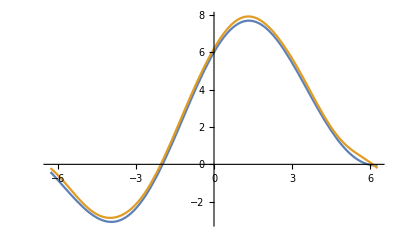

```mathematica
k=5;
Plot[{r[x],newFun[x]},{x,-2*Pi,2*Pi}]
```